# Mathematica as a Tool for Astronomy and Physics

## Lecture 7 Wintersemester 2009/10 Markus Röllig

## Plotting - continuation

Required Reading

Basic Plotting
Graphics and Sound
Data Visualization
Function Visualization

### Combining Plots

Required Reading

Redrawing and Combining Plots
Combining Graphics
Grids, Rows, and Columns
Insetting Objects in Graphics

You can use the Show to either show a plot with an alternative set of options:
Show[graphics,options] or you can combine several plots in one.
Show[g_1,g_2,…] shows several graphics combined.

```mathematica
Plot[Sin[x^2]/x,{x,0,10}]
```

Now we change the options a little:

```mathematica
Show[%,PlotRange->{{8,10},{-.3,.3}},AxesOrigin->{8.0,0}]
```

```mathematica
{DensityPlot[Sin[x]Sin[y],{x,-3,3},{y,-3,3}],ContourPlot[Sin[x]Sin[y],{x,-3,3},{y,-3,3},ContourShading->None]}
```

```mathematica
Show[%[[1]],%[[2]]]
```

When combining two plots, Mathematica again produces a Graphics object with the already known structure:

```mathematica
i1 = ParametricPlot[
Evaluate[{+2, +3} + (-1 +0.5 Sqrt[Abs[φ]]) {Cos[φ], Sin[φ]}],
                        {φ, -4Pi, 4Pi}]

i2 = ParametricPlot[
Evaluate[{-5, -5} + (-1 - 3 Log@Sqrt[Abs[φ]]) {Cos[φ], Sin[φ]}],
                        {φ, -3Pi, 3Pi}, PlotPoints -> 500]
```

```mathematica
Show[i1, i2, PlotRange -> All]
```

The resulting Graphics-object consists of two separate lines along with the values of the options. The two lines are also contained in List, which is necessary to pass on any graphics directives, such as thickness and color.

```mathematica
InputForm[% /. {Line[_] ->"longLine"}]
```

When you combine multiple plots using Show without any further options, then Mathematica uses the PlotRange from the first plot! This might cut off interesting parts of the remaining plots. The order is important here.

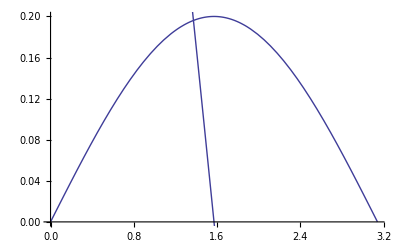
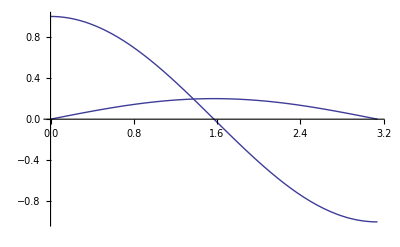

```mathematica
{Show[{Plot[0.2Sin[x],{x,0,Pi}],Plot[Cos[x],{x,0,Pi}]}],Show[{Plot[Cos[x],{x,0,Pi}],Plot[0.2Sin[x],{x,0,Pi}]}]}
```

You can also Inset one graphic object into another

```mathematica
in=Plot[Cos[x],{x,-3 Pi,3Pi},ImageSize->100,Frame->True];
Plot[Sin[x] /x,{x,-3 Pi,3Pi},Epilog->Inset[in,{6,0.6}]]
```

You can arrange multiple plots in Grids, Rows and Columns

GraphicsRow[{g_1,g_2,…}] generates a graphic in which the g_i are laid out in a row.

GraphicsColumn[{g_1,g_2,…}]generates a graphic in which the g_i are laid out in a column, with g_1 above g_2, etc.

GraphicsGrid[{{g_11,g_12,…},…}]generates a graphic in which the g_ij are laid out in a two-dimensional grid.

```mathematica
$TrigFunctions={Sin,Cos,Sec,Csc};
Table[Plot3D[Abs[f[x+I y]],{x,-2,2},{y,-2,2},MeshFunctions->Function@@@{{{x,y,z},Re[f[x+I y]]},{{x,y,z},Im[f[x+I y]]}},MeshStyle->{Orange,Green},PlotLabel->f,Ticks->None],{f,$TrigFunctions}];
GraphicsRow[%]
GraphicsColumn[%%]
GraphicsGrid[{%%%[[1;;2]],%%%[[3;;4]]}]
```

#### Excercise

Create a 3x2 array of plots. Adapt the ImageSize so that all plots fit on your screen.

What happens when you use Show to combine the two plots:
Plot[x,{x,0,5}] and Plot[x,{x,-5,0}]. pay attention to the resulting x- and y-range.

Use GraphicsRow to plot the two plots from the excercise before in a row and draw frames around each plot.

Instead of GraphicsRow use Row. What are the differences?

Plot a function of your choice and write the function in a corner of the plot.

### Logarithmic Plots

Plot uses a decimal axis scale. You can use logarithmic scales using the following commands:
LogPlot, LogLinearPlot, LogLogPlot

```mathematica
f[x_]:=Exp[-x]+4 Exp[-2x]
```

```mathematica
{Plot[f[x],{x,1,6}],LogPlot[f[x],{x,1,6}],LogLinearPlot[f[x],{x,1,6}],LogLogPlot[f[x],{x,1,6}]}
```

LogPlot effectively generates a curve based on Log[f], but with tick marks indicating the values of the underlying function f.

```mathematica
{LogPlot[x^Sin[x],{x,0,10}],Plot[Log[x^Sin[x]],{x,0,10},AxesOrigin->{0,-1.5}]}
```

Mathematica uses a special set of rules to determine which ticks to draw in logarithmic plots. The result may not be what you might want for publication ready plots. Sometimes you will need to use custom ticks to produce the desired results. Sometimes it is just the tick mark labels that are not what you might want.

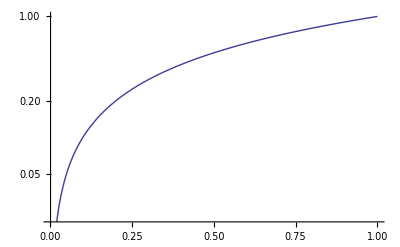

```mathematica
LogLogPlot[x,{x,0.001,1}]
```

For ranges of more than 6 dex the ticks and labels are placed very unconveniently:

```mathematica
LogLogPlot[x,{x,1,10^7}]
```

```mathematica
LogLogPlot[x,{x,1,10^6}]
```

Take a look at the 'true' coordinates of a log-plot.

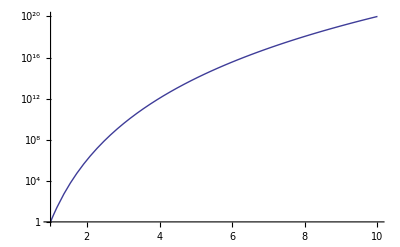

```mathematica
LogPlot[x^20,{x,1,10}]
```

The y-value 10^20is drawn at the plot y-value of 46.051701859880914.

```mathematica
InputForm[Options[LogPlot[x^20,{x,1,10}]]]//Short[#,10]&
```

{Ticks -> {Automatic, {{0, 1}, {9.210340371976184, Superscript[10, 4]}, {18.420680743952367, Superscript[10, 8]}, {27.631021115928547, Superscript[10, 12]}, {36.841361487904734, Superscript[10, 16]}, {46.051701859880914, Superscript[10, 20]}, {7.013915474810528, "", {0.00375, 0.}, {Thickness[0.001]}}, {<<4>>}, <<34>>, {45.46399519177896, "", {0.00375, 0.}, {Thickness[0.001]}}, {45.64628675052279, "", {0.00375, 0.}, {Thickness[0.001]}}, {45.80041600262042, "", {0.00375, 0.}, {Thickness[0.001]}}, {45.93393132414641, "", {0.00375, 0.}, {Thickness[0.001]}}}}, <<14>>}

This is ln(10^20)

```mathematica
Log[10^20]//N
```

46.0517

Imagine you want to write some text in the plot. You can use Epilog to do this, but beware the coordinates:

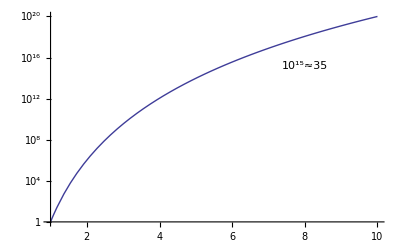

```mathematica
LogPlot[x^20,{x,1,10},Epilog->Text["10^15≈35", {8,35}]]
```

#### Excercises

Plot the following list of Points logarithmically: Table[Power10,i],{i,1,10}]

Plot f(x)= sin(x)exp(x) from x=[0,100]

Use Show to combine two log-log Plots.

### Plotting a function of two variables

Required Reading

Density and Contour Plots
Parametric Plots

An explicit function of two independent variables can be displayed using Plot3D.  The basic syntax is Plot3D[f,{x,xmin,xmax},{y,ymin,ymax}].

```mathematica
Plot3D[Im[ArcSin[(x+I y)^4]],{x,-2,2},{y,-2,2},PlotPoints->50,PlotStyle->Directive[Pink,Specularity[White,50],Opacity[0.8]]]
```

Contour or density plots often prove very useful in locating extrema, ridges, or other important features of functions of two or more dimensions.  These plots can also help in finding starting points for numerical solution of equations.

DensityPlot[f,{x,x_min,x_max},{y,y_min,y_max}] make a density plot of f
ContourPlot[f,{x,x_min,x_max},{y,y_min,y_max}] make a contour plot of f as a function of x and y

```mathematica
DensityPlot[Sin[x] Sin[y],{x,-2,2},{y,-2,2},ColorFunction->ColorData["SolarColors"]]
```

Move with the mouse over the contours in the following contour plot. The default style is to add a tooltip to indicate the contour level.

```mathematica
ContourPlot[Sin[x] Sin[y],{x,-2,2},{y,-2,2}]
```

```mathematica
ContourPlot[Sin[x]Sin[y],{x,-2,2},{y,-2,2},ContourLabels->True]
```

A speciality is the ability ofg contour plot to plot implicit plots,

```mathematica
ContourPlot[x^2+y^2==1,{x, -1,1},{y,-1,1}]
```

```mathematica
ContourPlot[Sin[x] Sin[y]==0.2,{x,-3,3},{y,-3,3}]
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u.

#### Excercises

Plot the curve described by the parametric equations {x=r (1-sin(t)), y=r (1-cos(t))} for the interval {t,-2π,2π}.

Use Plot3D to draw the surface f(x,y)=Exp(-y^2)sin(x)-1 in the box region -2≤x≤2, -2≤y≤2.Then use ContourPlot to display the surface contours. Use ContourPlot to you visualize the solution f(x,y)=-0.9?

### Special Plots

Required Reading

Some Special Plots

The Plot command is used to plot functions in the form y=f[x]. Mathematica also understands parametrized formulation of functions. ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u.

This is the parameter form of a circle:

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]
```

Another plot with a more random appearance

```mathematica
ParametricPlot[Evaluate @ 
Table[Sum[Sin[i + j] Cos[i t + Pi Sin[i]], 
          {i, 17}], {j, 1, 2}], {t, 0,2 Pi}, 
   PlotRange -> All, Frame -> True, PlotPoints -> 5000,
   Axes -> False, AspectRatio -> Automatic]
```

Plot multiple functions

```mathematica
ParametricPlot[{{Sin[u],Sin[2u]},{1/2Cos[u],1/2Sin[u]}},{u,0,2Pi}]
```

An interesting feature is the capability to plot parametric regions: ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}]

```mathematica
ParametricPlot[{r Cos[t],r Sin[t]},{t,0,2Pi},{r,0.5,1},Mesh->False]
```

```mathematica
ParametricPlot[Evaluate[
     (Exp[Cos[σ]] - 2Cos[4 σ] + Sin[σ/12]^5) {Cos[σ], Sin[σ]}],
     {σ, 0, 2Pi}, AspectRatio -> Automatic, Axes -> None]
```

Remember our function to replace points with scaled and rotated rectangles? ParametricPlot also produces a list of points to be connected with lines, hence:

```mathematica
convertToRectangles[%]
```

The 3-dim counterpart is of course ParametricPlot3D[{f_x,f_y,f_z},{u,u_min,u_max}].

```mathematica
pl=ParametricPlot3D[{(2+Cos[8u])Cos[u],(2+Cos[8u])Sin[u],Sin[8u]},{u,0,2Pi}]
```

convertToRectangles ??

In 3-dim a rectangle becomes a cuboid. The upgrade of our playground routine is more or less straight forward. We omitted the rotation part and used oppacity to make the inner 2 cuboids visible. However, this makes the rendering quite slow.

```mathematica
Remove[convertToCuboids]
convertToCuboids[plot_]:=Graphics3D[Table[Table[{Opacity[1/j],Hue[i/(Length@#)j],Scale[Cuboid[#[[i]][[1]],#[[i]][[2]]],j]},{j,3,1,-1}],{i,1,Length@#}]&[Partition[plot[[1,1,3,2,1]],2,1]]]
```

```mathematica
convertToCuboids[pl]
```

Another example from the Mathematica Guide Books:

```mathematica
f = (2 + Cos[u/2] Sin[t] - Sin[u/2] Sin[2t]) Cos[u];
g = (2 + Cos[u/2] Sin[t] - Sin[u/2] Sin[2t]) Sin[u];
h = Sin[u/2] Sin[t] + Cos[u/2] Sin[2t];

ParametricPlot3D[{f, g, h},
                 {t, 0, 2Pi}, {u, 0, 2Pi},ColorFunction->Function[{x,y,z,u,t},Hue[(t + u)/(4Pi)]],Boxed -> False,Axes -> None]
Remove[f,g,h,pl]
```

PolarPlot[r,{θ,θ_min,θ_max}]  generates a polar plot of a curve with radius r as a function of angle θ.

```mathematica
PolarPlot[Sin[Pi t^2],{t,0,Pi}]
```

ListPolarPlot[{r_1,r_2,…}] plots points equally spaced in angle at radii r_i.

```mathematica
butterfly[λ_][p_,o___]:=ListPolarPlot[Table[{θ,(Exp[Cos[θ]]-2Cos[4θ])Sin[λ θ]^4},{θ,0,2Pi,p}],o,PlotRange->All,PlotStyle->PointSize[Tiny]]
```

```mathematica
butterfly[99999999][0.00055]
```

```mathematica
butterfly[99999999][0.0005]
```

SphericalPlot3D[r,θ,ϕ]generates a 3D plot with a spherical radius r as a function of spherical coordinates θ and ϕ.

```mathematica
SphericalPlot3D[ϕ+ Sin[7θ],θ,ϕ]
```

SphericalPlot3D[r,{θ,θ_min,θ_max},{ϕ,ϕ_min,ϕ_max}] generates a 3D spherical plot over the specifed ranges of spherical coordinates.

```mathematica
SphericalPlot3D[1,{θ,0,Pi},{ϕ,0,3/2Pi}]
```

RevolutionPlot3D[f_z,{t,t_min,t_max}]  generates a plot of the surface of revolution with height f_z at radius t. Revolve a function curve around the z axis:

```mathematica
RevolutionPlot3D[t^3-t^2,{t,0,1}]
```

Here is a nice example of what can be done with it:

```mathematica
{RevolutionPlot3D[{Sin[t]+Sin[5t]/10,Cos[t]+Cos[5t]/10},{t,0,Pi}],
RevolutionPlot3D[{Sin[t]+Sin[5t]/10,Cos[t]+Cos[5t]/10},{t,0,Pi},RegionFunction->Function[{x,y,z,t,θ,r},Sin[8t]Sin[8θ]>0.1],Mesh->None,PlotStyle->FaceForm[Red,Cyan],PlotPoints->35,BoundaryStyle->Black]}
```

DateListPlot[{{date_1,v_1},{date_2,v_2},…}]plots points with values v_i at a sequence of dates.

```mathematica
DateListPlot[{{{2006,10,1},10},{{2006,10,15},12},{{2006,10,30},15}, {{2006,11,20},20}}]
```

Example :Retrieve and plot a historical stock price:

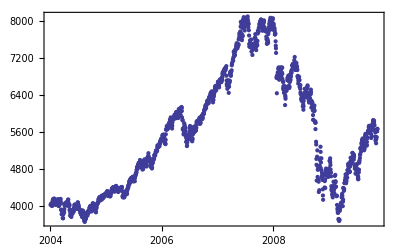

```mathematica
DateListPlot[FinancialData["DAX","Jan. 1, 2004"]]
```

#### Excercises

Plot a Logarithmic spirals of the form r=a ⅇ^(b θ)

Plot a four-leaved rose, r=cos^2 θ-sin^2 θ

Plot a cardoid r = 1 + sinθ

Plot a limaçon, r=1/2+ cosθ

### Labeling your plots

Required Reading:

Annotating & Combining Graphics

Especially when plotting multiple functions or datasets in a single graph it is important to clearly label each function or data set. One way to do so is to use text labels in the plot. We can use the Epilog option to do so:

```mathematica
Plot[{20Exp[.01 t], 12Exp[.03 t]},{t,0,40},
AxesOrigin->{0,0},
Epilog->{Text[Style["Factory A", FontSize->18],(* now the coordinates *){5,25}],
Text["Factory B",{5,10}]}
]
```

Alternatively you can use the function Tooltip to provide "mouseover" labels. These are labels that will appear only when the mouse is moved over a certain feature. Example:

```mathematica
Tooltip[x+y,"label"]
```

Our plot may be labels accordingly:

```mathematica
Plot[{
Tooltip[20Exp[.01 t],"Factory A"],
Tooltip[12Exp[.03 t],"Factory B"]},
{t,0,40},
AxesOrigin->{0,0}
] (* move the mouse over the curves *)
```

This is especially nice for ListPlot. You can use it to distinguish between datasets:

```mathematica
ListPlot[{Tooltip[(3/2)^Range[15],TraditionalForm[(3/2)^k]],Tooltip[Fibonacci[Range[15]],TraditionalForm[Fibonacci[k]]]},PlotStyle->PointSize[Medium]]
```

Or you can use Tooltip to indicate the value of individual datapoints:

```mathematica
ListPlot[Table[Tooltip[Prime[i]],{i,10}]]
```

#### Excercise

Plot a random list of 10 integers between 1 and 100 and use tooltip to give the binary form of the numbers when moving the mouse over the data points

### Plots with Legend

```mathematica
Needs["PlotLegends`"]
```

Required Reading

Plot Legends Package

To include plot legends, you need to load an additional package. But even then, the Mathematica's legend capabilities are lacking.

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2 π,2 π},PlotLegend->{"Sine","Cosine"}]
```

We can change thy style somewhat:

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2 π,2 π},PlotLegend->{"Sine","Cosine"},LegendShadow->None, LegendSize->0.5,LegendPosition->{1.2,0}]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2 π,2 π},PlotStyle->{Directive[Purple,Thick],Directive[Thick,Orange,Dashing[{.03}]]},PlotLegend->{"sin","cos"},LegendPosition->{.5,-.8},LegendTextSpace->0.5,LegendLabel->Style["Trig Funcs",14],LegendLabelSpace->.5,LegendOrientation->Vertical,LegendBackground->LightPurple,LegendShadow->{.02,-.02},Background->LightOrange,LegendSize->{0.5,0.5}]
```

The second way of placing a legend in a graphic is to use ShowLegend. With ShowLegend you specify the graphic and legend as arguments.

```mathematica
ShowLegend[DensityPlot[Sin[x y],{x,0,π},{y,0,π}],{ColorData["LakeColors"][1-#1]&,10," 1","-1",LegendPosition->{1.1,-0.4}}]
```

```mathematica
ShowLegend[Plot3D[Sin[x y],{x,0,π},{y,0,π},ColorFunction->"Rainbow"],{ColorData["Rainbow"][1-#1]&,10," 1","-1",LegendPosition->{1.1,-0.4}}]
```

#### Custom Legend 1

It is also possible to construct your own legends:

```mathematica
Clear[legendPlot]
legendPlot[xl_List,d_,args___]:=Plot[xl,d,Epilog->Inset[Panel[Grid[MapIndexed[{Graphics[{ColorData[1,First@#2],Thick,Line[{{0,0},{1,0}}]},AspectRatio->.1,ImageSize->20],#1}&,xl]]],Offset[{-2,-2},Scaled[{1,1}]],{Right,Top}],args]
```

```mathematica
legendPlot[{Sin[x],Cos[x],Sinc[x]},{x,0,10}]
```

#### Custom Legend 2

Another way to create custom legends is here

```mathematica
Clear[legend];
legend[list_,pos_]:=Inset[Panel[Grid[MapIndexed[{Graphics[{ColorData[1,First@#2],Thick,Line[{{0,0},{1,0}}]},AspectRatio->.1,ImageSize->20],#1}&,list]]],pos,{Left,Top}];
```

```mathematica
Plot[{Re[PrimeZetaP[t]],Im[PrimeZetaP[t]]},{t,0.01,1},Epilog->{legend[{Re[PrimeZetaP[t]],Im[PrimeZetaP[t]]},Scaled[{0.1,0.9}]]}]
```

### Saving and Printing Graphics

When you want to save a graphic or print it you can use varios approaches. Take an example plot:

```mathematica
ListPolarPlot[Table[Sqrt[n],{n,100}],ImageSize->100]
```

If you click on the graph a reddish selection border appears. The use File ⊳ Print Selection ... to print the graph or use  File ⊳ Save Selection As ... to export your image as EPS, JPG or any other available data format. You can also click on the right output brackets to select the output cell and either use the right mouse click to save/print or use the menu items as above.

To be honest, Mathematica's printing and exporting capabilities is still somewhat lacking. Sometimes it might be necessary to save your graphics as PDF and then print it from acrobat viewer to get a nice printout. Wolfram aknowledges this deficit and promised improvements in the next releases.

### Excercises

#### Customize your Plots

Reproduce the following graph from  Cool Infographics

#### Customize your Plots II

Reproduce the following Business Week plot as good as possible:

The data points are: {2.9,2.45,2.5,3.5,3.7,3.0,1.75,0.75,0.3,0.2,1.9,1.6,0.5,-0.5,-2.8}

#### 4D data visualization

Consider possibilities to plot a 4-dim dataset. Use the following data:

```mathematica
(rad:=2Random[]-1;
data=Table[{xvar=rad,yvar=rad,zvar=rad,Abs[xvar yvar zvar]},{100}];)
```

#### Fourier-sine approximation to square wave

A square wave with unit amplitude and period 2π is defined by f[x+m π]=f[x] for any integer m and f[x]=Sign[x] for |x|<π.  This square wave can be approximated by a Fourier-sine series of the form

(f̃)_n[x]= 4/π  ∑_(k=1)^n Sin[(2k-1)x]/(2k-1)

where n is the order of approximation.  Produce a 2×3 graphics array which compares the first 6 approximations with the square-wave itself.

#### Antenna patterns

The angular distribution  of intensity produced by an array of n identical equally-spaced antennas which broadcast in phase at wave length λ has the form
f[n,d,λ,θ]=Sin[n π d/λ Sin[θ]]^2/Sin[π d/λ Sin[θ]]^2
where d is the spacing and θ the polar angle.  Use PolarPlot to display antenna patterns for n=4 and d/λ={1,4}.

#### Hydrogenic wave functions

Wave functions for the hydrogen atom take the form
ψ_(n,ℓ, m)(r,θ,ϕ)∝ⅇ^(-κ r) (κ r)^ℓ L_(n-ℓ-1)^(2 ℓ+1)(2 κ r) Y_ℓ^m(θ,ϕ)
where n is the principal (radial) quantum number, ℓ is the orbital angular momentum in units of ℏ, m is the magnetic (azimuthal) quantum number, and ℏ κ=√(2 μ E_b)is the wave number for positive binding energy E_b.  The radial dependence involves generalized Laguerre functions and the angular dependence spherical harmonics.  Note that we are not interested in the normalization of these functions at this time.  The probability density is given by the absolute square of the wave function, namely (|ψ|)^2.  Write a function that plots the probability density in the xy plane (θ=π/2) given values of the quantum numbers nℓm using Plot3D.   You will need to express the Cartesian coordinates in terms of spherical coordinates.  Write a similar function that uses DensityPlot.  Show several cases of each.

#### Sampling points

Write a function which displays the points sampled by Mathematica 's adaptive algorithm for Plot as vertical bars between the x-axis and the points themselves.

#### Potential and field for uniform sphere

The electric field of a uniformly charged sphere or the gravitational field of a sphere of uniform density both have the same shape.  Let ϕ=3/2-r^2/2 for r≤1 or ϕ=r^-1 for r≥1 represent the normalized potential, where r=√(x^2+y^2+z^2) is the distance from the center in units of the radius of the sphere.  The field if then f⃗=-OverVector[∇]ϕ.
a) Use ContourPlot to display equipotential lines in the xy plane (two-dimensions).
b) Use VectorPlot to display the force field in the xy plane.  Combine this plot with the equipotentials from the preceding exercise.
c) Use ContourPlot3D and VectorPlot3D to display equipotential surfaces and the vector field within a representative volume of space.

## Programming Intro

Required Reading

Mathematica Programming

Putting several commands together to accomplish some purpose beyond the capacity  of one individually means, you are programming. We already saw that parantheses () can be used to chain commands together:

```mathematica
f[x_]:=(Print["You entered:",x];Sin[x])
```

```mathematica
f[10]
```

Mathematica offers many programming constructs also known in other languages.

### Scoping - localizing variables

Required Reading:

Modularity and the Naming of Things

#### Iterator localization

When using a command that takes an iterator as argument, Mathematica will localize the iterator:

```mathematica
Remove[n]
Table[n,{n,1,10}]
n
```

```mathematica
n=4
Table[n,{n,1,10}]
n
Remove[n]
```

Other commands, that take iterators are Sum, Product, Integrate, etc..

#### With

Required Reading:

Local Constants

With allows you to define local constants.  With[{x=x_0,y=y_0,…},expr] specifies that in expr occurrences of the symbols x, y, …  should be replaced by x_0, y_0, … .

```mathematica
n=10;
Graphics[Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,2 Pi/n}]]]
```

```mathematica
Solve[3n+1==22,n]
```

```mathematica
Clear[n]
With[{n=5},Graphics[Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,2 Pi/n}]]]]
```

```mathematica
Solve[3n+1==22,n]
```

Definitions outside of the With construct are kept.

```mathematica
n=10;
With[{n=5},Graphics[Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,2 Pi/n}]]]]
n
```

The way With[{x=x_0,…},body] works is to take body, and replace every occurrence of x, etc. in it by x_0, etc. You can think of With as a generalization of the /. operator, suitable for application to Mathematica code instead of other expressions.

#### Module

Required Reading:

Modules and Local Variables
How Modules Work

Mathematica normally assumes that all your variables are global. This means that every time you use a name like x, Mathematica normally assumes that you are referring to the same object.

Particularly when you write programs, however, you may not want all your variables to be global. You may, for example, want to use the name x to refer to two quite different variables in two different programs. In this case, you need the x in each program to be treated as a local variable.

You can set up local variables in Mathematica using modules. Within each module, you can give a list of variables which are to be treated as local to the module.

Module[{x,y,…},body] a module with local variables x, y, …

```mathematica
t=17
```

```mathematica
Module[{t},t=8;Print[t]]
```

```mathematica
t
```

You can also give initial values to the localized variables: Module[{x=x_0,y=y_0,…},body]

The way modules work in Mathematica is basically very simple. Every time any module is used, a new symbol is created to represent each of its local variables. The new symbol is given a unique name which cannot conflict with any other names. The name is formed by taking the name you specify for the local variable, followed by $, with a unique "serial number" appended.

```mathematica
Module[{t},Print[t]]
```

```mathematica
Module[{t},Print[t]]
```

An important point to note is that Module[vars,body] inserts generated symbols only into the actual expression body. It does not, for example, insert such symbols into code that is called from body, but does not explicitly appear in body.

Since x does not appear explicitly in the body of the module, the local value is not used.

```mathematica
tmp=x^2+1;Module[{x=4},tmp]
```

Module is one of the main commands to built up complex commands.

```mathematica
fib[n_]:=
Module[{f},
f[1]=f[2]=1;
f[i_]:=f[i]=f[i-1]+f[i-2];
f[n]
]
```

The following example is taken from Michael Trott's Mathematica Guidebooks.

The following routine linePicture takes a list of n points (n is even) and generates all polygons with n+2 points that come from mirroring n/2 points on the line through midpoints of opposite line segments. This process is iterated iter times.

```mathematica
linePicture[startPolitList_?(EvenQ[Length[#]]&),iter_Integer?Positive]:=Module[{mirror,step},mirror[p_,{p1_,p2_}]:=(* mirrors p on line p1p2 *)Function[{d,e},p1-d+2(d.e) e][p-p1,(#/Sqrt[#.#])&[p2-p1]];
step[pList1_]:=(* mirrors one half of the n-gon on line
                  through two midpoints of two line segments *)Module[{pList,pn1,pn2,l=Length[pList1]},Table[(* go through all line segments *)pList=RotateRight[pList1,i];
(* the points for the mirror line *)pn1=(First[pList]+Last[pList])/2;
pn2=(pList[[l/2]]+pList[[l/2+1]])/2;
(* the new n-gon *)Join[{pn1},mirror[#,{pn1,pn2}]&/@Take[pList,{1,l/2}],{pn2},Take[pList,{l/2+1,l}]],{i,l}]];
(* make the picture *)Show[Graphics[{Thickness[0.001],(* make closed line by appending first point *)Map[Line[Append[#,First[#]]&[#]]&,(* iterate the construction *)NestList[Flatten[step/@#,1]&,{N[startPolitList]},iter],{-3}]}],AspectRatio->Automatic,PlotRange->All]]
```

First simple example:

```mathematica
linePicture[{{-1., 0}, {0, -1}, {1., 0.}, {0., 4.}}, 2]
```

The next example starts more complicated with a regular 22-gon

```mathematica
linePicture[Table[N[{Cos[φ], Sin[φ]}], 
                  {φ, 0, 2Pi (1 - 1/22), 2Pi/22}], 2]
```

#### Block

Required Reading:

Blocks and Local Values
Blocks Compared with Modules

Modules in Mathematica allow you to treat the names of variables as local. Sometimes, however, you want the names to be global, but values to be local. You can do this in Mathematica using Block.

Block[{x,y,…},expr] specifies that expr is to be evaluated with local values for the symbols x, y, … 
Block[{x=x_0,…},expr] defines initial local values for x, … .

Block allows you to set up an environment in which the values of variables can temporarily be changed. When you execute a block, values assigned to x, y, … are cleared. When the execution of the block is finished, the original values of these symbols are restored.

```mathematica
t=17
```

```mathematica
Module[{t},Print[t]]
```

```mathematica
Block[{t},Print[t]]
```

```mathematica
Block[{t},t=6;t^4+1]
```

```mathematica
t
```

Most traditional computer languages use a so-called "lexical scoping" mechanism for variables, which is analogous to the module mechanism in Mathematica. Some symbolic computer languages such as LISP also allow "dynamic scoping", analogous to Mathematica blocks.

When lexical scoping is used, variables are treated as local to a particular section of the code in a program. In dynamic scoping, the values of variables are local to a part of the execution history of the program.

This defines m in terms of i

```mathematica
m=i^2
```

The local value for i in the block is used throughout the evaluation of i+m.

```mathematica
Block[{i=a},i+m]
```

Here only the i that appears explicitly in i+m is treated as a local variable.

```mathematica
Module[{i=a},i+m]
```

We finish with a beautiful example from the Mathematica Guidebooks.

We define the recursive function:
V_r(x)=1/2(V_(r-1)(x))^2+(V_(r-1)(x^2))/(1-∑_(k=0)^(r-1) V_k(x))
V_0(x)=x.

```mathematica
𝒱[n_Integer, x_] := 
Block[{V},
      V[0, z_] := z;
      V[r_, z_] := V[r, z] = 
      1/2 (V[r - 1, z]^2 + V[r - 1, z^2])/
                      (1 - Sum[V[k, z], {k, 0, r - 1}]);
      (* calculate value with actual n and V *)
      V[n, x]]
```

After leaving the Block, all definitions made for V are no longer existent. Avoiding too many cached values is sometimes of importance for memory reasons. Without the above Block[{...}, localDefinitionsWithCaching], the following graphic displaying the phase of 𝒱[6, z] over the complex z-plane would accumulate more than three million cached values.

```mathematica
ContourPlot[Arg[𝒱[6, x + I y]]^2/Pi^2, {y, -2, 2}, {x, -2, 2},
ColorFunction -> (Hue[0.8 #]&),
PlotRange -> All,
Contours -> 20,
PerformanceGoal->"Speed",
ColorFunctionScaling -> False,
ContourLines -> False,PlotPoints->30](* CHANGE THE NUMBER OF PLOT POINTS *)
```

### Control Structures

Required Reading:

Loops and Control Structures
Conditionals tutorial
Conditionals Guide
Piecewise Functions

Mathematica provides various ways to set up conditionals, which specify that particular expressions should be evaluated only if certain conditions hold.

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

```mathematica
If[Pi^2>ⅇ^2,π,ⅇ]
```

```mathematica
If[π∈Reals,t,f]
```

```mathematica
If[π∈Rationals,t,f]
```

```mathematica
If[PrimeQ[10^100+1],t,f]
```

```mathematica
f[x_]:=If[x<0, Cos[x],Cos[x]/(Exp[x])]
```

```mathematica
Plot[f[x],{x,-10,10}]
```

The function If provides a way to choose between two alternatives. Often, however, there will be more than two alternatives. One way to handle this is to use a nested set of If functions. Usually, however, it is instead better to use functions like Which and Switch.

Which[test_1,value_1,test_2,value_2,…]evaluates each of the test_i in turn, returning the value of the value_i corresponding to the first one that yields True.

This defines a function with three regions. Using True as the third test makes this the default case.

```mathematica
h[x_]:=Which[x<0,x^2,x>5,x^3,True,0]
```

```mathematica
h[-5]
h[2]
```

If you want to construct a conditional that does not depend on conditions but on forms/patterns you can use Switch[expr,form_1,value_1,form_2,value_2,…]which evaluates expr, then compares it with each of the form_i in turn, evaluating and returning the value_i corresponding to the first match found.

```mathematica
f[x_]:=Switch[x,_Integer,"Integer",_Rational,"Rational",_Real,"Real",_Complex,"Complex",_Symbol,"Symbol",_,"something else"]
```

```mathematica
f[x]
f[1]
f[π]
f[3/2]
f[2+I 4]
```

### Loops

I want to start this section with a quote from the Mathematica Guidebooks by Michael Trott:

Constructions that use For, While, and Do in other programming languages can often be implemented in Mathematica in a cleaner, more elegant, and faster-executing way using list operations like Map, Thread, (all to be discussed in the next chapter) and so on and Fold, FoldList, Nest, NestList, FixedPointList, and FixedPoint....

Required Reading:

Loops and Control Structures
Repetitive Operations

The execution of a Mathematica program involves the evaluation of a sequence of Mathematica expressions. In simple programs, the expressions to be evaluated may be separated by semicolons, and evaluated one after another. Often, however, you need to evaluate expressions several times, in some kind of "loop".

Do[expr,{i,i_min,i_max}] evaluates expr with the variable i successively taking on the values i_min through i_max (in steps of 1). Do uses the standard Mathematica iteration specification.

```mathematica
Do[Print[n^2],{n,4}]
```

This loops over values of i from 1 to 4, and for each value of i, loops over j from 1 to i-1.

```mathematica
Do[Print[{i,j}],{i,4},{j,i-1}]
```

Sometimes you may want to repeat a particular operation a certain number of times, without changing the value of an iteration variable. You can specify this kind of repetition in Do just as you can in Table and other iteration functions.

```mathematica
t=x;Do[t=1/(1+t),{3}];t
```

As in other programming languages, a calculation can be repeated based on a test using While and For.

While[test,body]evaluates test, then body, repetitively, until test first fails to give True. Example: Print and increment n while the condition n<4 is satisfied:

```mathematica
n=1;While[n<4,Print[n];n++]
```

Break breaks out of the While:

```mathematica
n=1;While[True,If[n>10,Break[]];n++]
n
```

For[start,test,incr,body]executes start, then repeatedly evaluates body and incr until test fails to give True. The sequence of evaluation is test, body, incr. For exits as soon as test fails.

This is a very common form for a For loop. i++ increments the value of i.

```mathematica
For[i=1,i<4,i++,Print[i]]
```

Here is a more complicated For loop. Notice that the loop terminates as soon as the test i^2<10 fails.

```mathematica
For[i=1;t=x,i^2<10,i++,t=t^2+i;Print[t]]
```

#### Example: Calculating the square root - Babylonian method

To calculate the value of √a  of a positive number a, we will use the Babylonian method, going back to Heron of Alexandria (10-70 AD). This is a quadratically convergent algorithm, which means that the number of correct digits of the approximation roughly doubles with each iteration. It proceeds as follows:

Let x be an estimate of √a

Then, the real value X will lie between a/x and x  (why?)

Taking  the mean between those will get us closer to X: 1/2(x+a/x)

As an example we take √2, ourt initial guess X=1.5:

```mathematica
Module[{a=2,x},x=1.5;x=1/2(x+a/x)]
```

1.41667

```mathematica
Sqrt[N[2]]
```

1.41421

If we repeat the last step we come closer to the real value:

```mathematica
Module[{a=2,x},x=1.5;x=1/2(x+a/x);x=1/2(x+a/x)]
```

1.41422

The iteration method is easily implemented in a loop.

```mathematica
Module[{a=2,x},x=1.5;Do[x=1/2(x+a/x),{3}];x//N]
```

1.41421

The exact value of the initial guess makes no big difference. We can start with x_initial=a and only loose one iteration step. To iterate until a given accuracy is met we use While:

```mathematica
mySqrt[a_]:=Module[
{x=a,},
While[Abs[x-a/x]>10^(-10),x=(x+a/x)/2];
x]
```

```mathematica
mySqrt[2.]
```

1.41421

#### Excercise

Create a loop that prints the first 20 positive integers. Find one realisation for each loop command from this section

Create a loop that prints the first 20 Powers of base 2. Find one realisation for each loop command from this section

Create a loop that prints the following sequence 1,2,4,7,11,16,22,29,...

Create a loop thatfinds all pairs {n,m} such that n^2+m^2is a square number (e.g. 3^2+4^2=5^2)

Find the first prime number consisting only of ones and is bigger than 11.

Find the sum of the sequence
1/(1+2)+2/(2+3)+...+10/(10+11)

Euclidean algorithm

In mathematics, the Euclidean algorithm (also called Euclid's algorithm) is an efficient method for computing the greatest common divisor (GCD), also known as the greatest common factor (GCF) or highest common factor (HCF). It is named after the Greek mathematician Euclid, who described it in Books VII and X of his Elements.

The GCD of two numbers a, b  is calculated by subtracting the smaller from the larger one, until both are the same. That number is the GCD.

Example a = 1071 and b = 462
1071-462 = 609
609 - 462 = 147
462 - 147 = 315
315 - 147 = 168
168 - 147 = 21
147 - 21 = 126
repeat 6 more times
-> 21-21=0
---> GCD(1071,462) = 21

```mathematica
GCD[1071,462]
```

21

Write a programm to calculate the GCD of two given integers

### Debugging - Trace

Required Reading:

Tracing Evaluation

In Mathematica the two most important commands for debugging are On and Trace.

On[symbol::tag] switches on a message, so that it can be printed.  On[] is equivalent to On[s::trace] for all symbols. Let's see an example:

```mathematica
On[]
x=π/3
Sin[π+x]
Off[]
```

On will give very long output. Often, Trace is much more appropriate than is On[]. Trace[expr] generates a list of all expressions used in the evaluation of expr.

```mathematica
Trace[x=π/3;Sin[π+x]]
FullForm[%]
Remove[x]
```

One advantage of Trace is that the output is a syntactically correct mathematica expression. We see in the FullForm of the Trace above that the subexpressions are enclosed in HoldForm. We can use Mathematica to analyse the output of Trace.

```mathematica
tr=Trace[integral=Integrate[Sin[x]*Cosh[x+π/2]*Log[x],x]]
```

```mathematica
{Depth[tr],ByteCount[tr],StringLength[ToString[FullForm[tr]]]}
```

TracePrint[expr] prints all expressions used in the evaluation of expr.

```mathematica
TracePrint[x=π/3;Sin[π+x]]
```

```mathematica
Trace[y=6;Plus[(y=y+1);5,y]]//TableForm
```

```mathematica
Trace[y=6;Plus[y,(y=y+1);5]]//TableForm
```

```mathematica
Module[{t=6,u=t},u^2]
```

```mathematica
Trace[Module[{t=6,u=t},u^2]]
```

### Application: Newton's Method

We want to apply the new information from this section to a well known method: finding a function's root using Newton's method. We will use the function x^3-30. The built in command to do this is FindRoot:

```mathematica
Remove[x]
FindRoot[x^2-30==0,{x,20}]
```

Newton's algorithm works as follows: given a function f

give an initial estimate of the root, say x_0

use the following rule to compute better estimates x_1, x_2, x_3, x_4,... until you are done:
x_(i+1)=x_i-(f(x_i))/(f'(x_i))

Doing it manually shows that already after 5 iterations we are quite close to the root:

```mathematica
f[x_]:=x^2-30
```

```mathematica
Subscript[x, 0]=20;
```

```mathematica
Subscript[x, 1]=Subscript[x, 0]-f[Subscript[x, 0]]/f'[Subscript[x, 0]]//N
```

```mathematica
Subscript[x, 2]=Subscript[x, 1]-f[Subscript[x, 1]]/f'[Subscript[x, 1]]//N
```

```mathematica
Subscript[x, 3]=Subscript[x, 2]-f[Subscript[x, 2]]/f'[Subscript[x, 2]]//N
```

```mathematica
Subscript[x, 4]=Subscript[x, 3]-f[Subscript[x, 3]]/f'[Subscript[x, 3]]//N
```

```mathematica
Subscript[x, 5]=Subscript[x, 4]-f[Subscript[x, 4]]/f'[Subscript[x, 4]]//N
```

```mathematica
xi=20;
Do[xi=N[xi-f[xi]/f'[xi]];Print[xi],{10}]
xi
```

If we don't know how many iterations we will need to come sufficiently close to the root we coudl use While to build the loop:

```mathematica
ε=10^-15;
xi=20;
While[Abs[f[xi]]>ε,xi=N[xi-f[xi]/f'[xi]];Print[xi]]
xi
```

Finally we can pluf it all together:

```mathematica
newton[function_,xinitial_,ε_]:=Module[{xi=xinitial},While[Abs[function[xi]]>ε,xi=N[xi-function[xi]/function'[xi]]];xi]
```

```mathematica
newton[f,40,10^-5]
```

### Excercise

Compute the square roots of 50 and 60 simultaneously, i.e. with a single Do loop.

Do is closely related to Table. The difference is that Do does not return any values, whereas Table does. Use Table instead of Do for the above excercise.

Improve the function newton. Try to reduce the number of function calls to f and the number of times that the derivative has to be calculated.

The Sieve of Eratosthenes
One of the oldes algorithms in computing history is the Sieve of Eratosthenes. This method is used to find all prime numbers below a given number n. The big advantage of this method is that it find primes without division. The algorithm can be summarized as follows:
to find all prime numbers less than an integer n:

1) create a list of the integers 1 through n
2) starting with p=2, cross out all multiples of p
3) increment p by 1 and cross out all multiples of p
4) repeat the previous step until p>√n

Create a short program to realize the Sieve of Eratosthenes.